## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="TPI";
fitLabel=rxnName;
dataFileName=rxnName;
KeqEquilibrator=1/9.31;

assumedUncertaintyFraction = 0.05;
removeInputFiles = True;
removeOutputFiles = True;
(* user will need to change this path *)
pathMASSFittingPackage = "/home/mrama/Dropbox/test bla/MASSef/";

mainFolder = "fit";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data_model.csv"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.csv"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.csv"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath, assumedUncertaintyFraction];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(dhap^c⇌g3p^c)^TPI

;

Structure: 2

Active sites: 2

Km Values:

Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
g3p | Null | 9000 | 8833
9167 | 1/s | 7.6 | 25 | teoahcl | 0.1 |

Inhibition Values:

Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Ki | 2-phosphoglycolate | 0.006 | 0.0057
0.0063 |  | Competitive | dhap | Null | M | 7.6 | 25 | teoahcl | 0.1 |

Activation Values:

Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
catalyticBranch={"E_TPI[c] + dhap[c] <=> E_TPI[c]&dhap",
				"E_TPI[c]&dhap <=> E_TPI[c]&g3p",
				"E_TPI[c]&g3p <=> E_TPI[c] + g3p[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((TPI^c)_^+dhap^c⇌(TPI^c&dhap^c)_^)^TPI1,((TPI^c&g3p^c)_^⇌(TPI^c)_^+g3p^c)^TPI2,((TPI^c&dhap^c)_^⇌(TPI^c&g3p^c)_^)^TPI3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((TPI^c)_^+dhap^c⇌(TPI^c&dhap^c)_^)^TPI1,Overscript[(TPI^c&g3p^c)_^⇌(TPI^c)_^+g3p^c, TPI2],((TPI^c&dhap^c)_^⇌(TPI^c&g3p^c)_^)^TPI3};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

### Setup King-Altman Equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};
```

```mathematica
{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyMaxTime, nActiveSites];
```

kcat for

kcat rev

km for

km rev

{dhap^c,g3p^c}

```mathematica
haldaneRatiosList
```

{(k_TPI1^⟶ k_TPI2^⟶ k_TPI3^⟶)/(k_TPI1^⟵ k_TPI2^⟵ k_TPI3^⟵)}

```mathematica
unifiedRateConstList
```

{}

### Setup King-Altmann Equations - old

```mathematica
(*{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;
simplifyMaxTime=300;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
eqRateConstSub={};


(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)

absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs, simplifyMaxTime, nActiveSites];


(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getEquivRateConsts[enzymeModel, eqRateConstSub, nonCatalyticReactions];

(*Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data*)
(*Simplify fixes Python evaluation issues dealing with fractional exponents (e.g.'(-1)**(3/5)' returns 1.0)*)
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub];


(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];*)
```

## Semi-Automated Simulate Data - old

### User Input Section

```mathematica
logStepSize=0.2;
(*nonKmParamWeight=3;*)
(*Weighting factor for non-Km data points. You can be specify this manually*)
{minPsDataVal, maxPsDataVal}= getMinMaxPsDataVal[1];
nonKmParamWeight=Length[Table[1,{i,minPsDataVal, maxPsDataVal,logStepSize}]];
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)
```

### Simulate data

```mathematica
pHandT={7.6, 25};
KeqEquilibrator=1/9.31;
kmFittingData= simulateKmData[rxn, metsFull,  metSatForSub, metSatRevSub, kmList, otherParmsList, assumedSaturatingConc, eTotal,
			   logStepSize,activeIsoSub, bufferInfo, ionCharge, inputPath,  fileList, KeqEquilibrator];


kcatFittingData=simulateKcatData[rxn, metsFull,  metSatForSub, metSatRevSub, kcatList, otherParmsList, assumedSaturatingConc, eTotal,
			  logStepSize, nonKmParamWeight, activeIsoSub, bufferInfo, ionCharge, inputPath, 
			  fileList, KeqEquilibrator];

haldane=haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
haldaneRatio=haldane[[2]];

{KeqFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[haldaneRatio,KeqEquilibrator, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT,"haldaneRatio"];
```

### Assemble and export All Data

```mathematica
header=Join[Map[ToString, metsSub[[All,1]]],{"FileFlag", "Target_Data"}];
fittingData = Flatten[{kmFittingData,kcatFittingData, KeqFittingData}, 1];

dataPath =FileNameJoin[{inputPath,dataFileName <>".dat"}, OperatingSystem->$OperatingSystem];

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
FilePrint[dataPath]
```

Keq_TPI	dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0.10741138560687433	0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/relRateRev_g3p.txt"	0.09090909090909087
0.10741138560687433	0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/relRateRev_g3p.txt"	0.13680688860321
0.10741138560687433	0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/relRateRev_g3p.txt"	0.20076000891310164
0.10741138560687433	0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/relRateRev_g3p.txt"	0.28474724895080133
0.10741138560687433	0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/relRateRev_g3p.txt"	0.3868631798468567
0.10741138560687433	0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/relRateRev_g3p.txt"	0.4999999999999999
0.10741138560687433	0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/relRateRev_g3p.txt"	0.613136820153143
0.10741138560687433	0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/relRateRev_g3p.txt"	0.7152527510491986
0.10741138560687433	0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/relRateRev_g3p.txt"	0.7992399910868982
0.10741138560687433	0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/relRateRev_g3p.txt"	0.8631931113967899
0.10741138560687433	0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/relRateRev_g3p.txt"	0.9090909090909091
0.10741138560687433	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/absRateRev.txt"	9000
0.10741138560687433	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/absRateRev.txt"	9000
0.10741138560687433	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/absRateRev.txt"	9000
0.10741138560687433	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/absRateRev.txt"	9000
0.10741138560687433	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/absRateRev.txt"	9000
0.10741138560687433	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/absRateRev.txt"	9000
0.10741138560687433	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/absRateRev.txt"	9000
0.10741138560687433	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/absRateRev.txt"	9000
0.10741138560687433	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/absRateRev.txt"	9000
0.10741138560687433	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/absRateRev.txt"	9000
0.10741138560687433	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/absRateRev.txt"	9000
0.10741138560687433	0	0	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/haldaneRatio.txt"	0.10741138560687433
0.10741138560687433	0	0	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/haldaneRatio.txt"	0.10741138560687433
0.10741138560687433	0	0	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/haldaneRatio.txt"	0.10741138560687433
0.10741138560687433	0	0	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/haldaneRatio.txt"	0.10741138560687433
0.10741138560687433	0	0	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/haldaneRatio.txt"	0.10741138560687433
0.10741138560687433	0	0	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/haldaneRatio.txt"	0.10741138560687433
0.10741138560687433	0	0	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/haldaneRatio.txt"	0.10741138560687433
0.10741138560687433	0	0	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/haldaneRatio.txt"	0.10741138560687433
0.10741138560687433	0	0	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/haldaneRatio.txt"	0.10741138560687433
0.10741138560687433	0	0	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/haldaneRatio.txt"	0.10741138560687433
0.10741138560687433	0	0	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit_dKd_GAPD/input/haldaneRatio.txt"	0.10741138560687433

## Semi-Automated Simulate Data

```mathematica
haldaneDataList=Table[
	{haldaneRatio, KeqEquilibrator,{0.9*KeqEquilibrator,1.1*KeqEquilibrator}},
{haldaneRatio, haldaneRatiosList}];

customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
Export["TPISimulateDataArguments.mx",{enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];
Export["TPISimulateDataResults.mx",{allFittingData, dataPath, fileList, fileListSub},"MX"];
```

```mathematica
{allFittingData, dataPath, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint@dataPath
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909087
0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860321
0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.3868631798468567
0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.4999999999999999
0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.613136820153143
0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.9090909090909091
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000

### Simulate data with uncertainty

```mathematica
Export["TPISimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["TPISimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[1]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10195128353443131
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10195128353443131
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10195128353443131
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10195128353443131
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10195128353443131
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10195128353443131
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10195128353443131
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10195128353443131
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10195128353443131
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10195128353443131
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10195128353443131
0	0.00008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909086
0	0.00013798244196800728	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860320997
0	0.00021868743295425528	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.0003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.38686317984685675
0	0.0008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.49999999999999983
0	0.001379824419680073	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.6131368201531431
0	0.002186874329542555	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.008706103516902621	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.909090909090909
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051

### Parameter scan

```mathematica
Export["TPIParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["TPIParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",2,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[5]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909087
0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860321
0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.3868631798468567
0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.4999999999999999
0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.613136820153143
0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.9090909090909091
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/relRateFor_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/relRateFor_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run a single fit on your local system without uncertainty

```mathematica
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python","\""<>runFitScriptPath <>"\"", "\""<>psoParameterPath <>"\"", "\""<>lmaParameterPath <>"\"", "\""<>psoTrialSummaryFileName <>"\"","\""<> psoResultsFileName <>"\"", "\""<>lmaResultsFileName <>"\"", ToString @numTrials, "\""<>dataPath <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"]
```

best_fit: 0.92747626493
best_fit: 0.262071936132
best_fit: 0.813147737769
best_fit: 1.04188661644
best_fit: 1.03651886642

### Run Fitting on your Local System with uncertainty or parameter scan

```mathematica
Do[
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python",
						"\""<>runFitScriptPath <>"\"",
						 "\""<>psoParameterPath <>"\"",
						 "\""<>lmaParameterPath <>"\"", 
						"\""<> StringTake[psoTrialSummaryFileName, ;;-5] <>"_"<>ToString[datasetI] <>".txt\"",
						"\""<> StringTake[psoResultsFileName, ;;-5] <>"_"<>ToString[datasetI] <>".txt\"",
						 "\""<>StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt\"", ToString @numTrials, 
						"\""<>dataPathList[[datasetI]] <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"] ,

{datasetI, 1, Length@dataPathList}];
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
lmaResultsFileName=lmaResultsFileName;
dataFilePath = dataPath;
```

```mathematica
splitChar = If[$OperatingSystem == "Windows", "\\", "/"];
resultsFileName = StringSplit[lmaResultsFileName, splitChar][[-1]];

fittingData=Import[dataFilePath];
fittingData = fittingData[[2;;,All]];
resultsFile = FileNameJoin[{"raw",resultsFileName}, OperatingSystem->$OperatingSystem];
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, True,""];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  | 
haldaneRatio_1 | 1.13437×10^-11 | 1.2868×10^-22 | 2.61198×10^-9 | 0.107411 | 0.107411
haldaneRatio_1 | 1.13437×10^-11 | 1.2868×10^-22 | 2.61198×10^-9 | 0.107411 | 0.107411
haldaneRatio_1 | 1.13437×10^-11 | 1.2868×10^-22 | 2.61198×10^-9 | 0.107411 | 0.107411
haldaneRatio_1 | 1.13437×10^-11 | 1.2868×10^-22 | 2.61198×10^-9 | 0.107411 | 0.107411
haldaneRatio_1 | 1.13437×10^-11 | 1.2868×10^-22 | 2.61198×10^-9 | 0.107411 | 0.107411
haldaneRatio_1 | 1.13437×10^-11 | 1.2868×10^-22 | 2.61198×10^-9 | 0.107411 | 0.107411
haldaneRatio_1 | 1.13437×10^-11 | 1.2868×10^-22 | 2.61198×10^-9 | 0.107411 | 0.107411
haldaneRatio_1 | 1.13437×10^-11 | 1.2868×10^-22 | 2.61198×10^-9 | 0.107411 | 0.107411
haldaneRatio_1 | 1.13437×10^-11 | 1.2868×10^-22 | 2.61198×10^-9 | 0.107411 | 0.107411
haldaneRatio_1 | 1.13437×10^-11 | 1.2868×10^-22 | 2.61198×10^-9 | 0.107411 | 0.107411
haldaneRatio_1 | 1.13437×10^-11 | 1.2868×10^-22 | 2.61198×10^-9 | 0.107411 | 0.107411
relRateRev_g3p | 5.18696×10^-12 | 2.69046×10^-23 | 1.19433×10^-9 | 0.0909091 | 0.0909091
relRateRev_g3p | 4.92517×10^-12 | 2.42573×10^-23 | 1.13405×10^-9 | 0.136807 | 0.136807
relRateRev_g3p | 4.56024×10^-12 | 2.07958×10^-23 | 1.05003×10^-9 | 0.20076 | 0.20076
relRateRev_g3p | 4.08085×10^-12 | 1.66533×10^-23 | 9.39673×10^-10 | 0.284747 | 0.284747
relRateRev_g3p | 3.49826×10^-12 | 1.22378×10^-23 | 8.05498×10^-10 | 0.386863 | 0.386863
relRateRev_g3p | 2.85277×10^-12 | 8.13832×10^-24 | 6.56875×10^-10 | 0.5 | 0.5
relRateRev_g3p | 2.20723×10^-12 | 4.87188×10^-24 | 5.08235×10^-10 | 0.613137 | 0.613137
relRateRev_g3p | 1.62467×10^-12 | 2.63956×10^-24 | 3.74098×10^-10 | 0.715253 | 0.715253
relRateRev_g3p | 1.1455×10^-12 | 1.31217×10^-24 | 2.63762×10^-10 | 0.79924 | 0.79924
relRateRev_g3p | 7.80556×10^-13 | 6.09268×10^-25 | 1.79731×10^-10 | 0.863193 | 0.863193
relRateRev_g3p | 5.1871×10^-13 | 2.6906×10^-25 | 1.19438×10^-10 | 0.909091 | 0.909091
absRateRev | 4.56923×10^-12 | 2.08779×10^-23 | 1.05218×10^-9 | 9000 | 9000.
absRateRev | 4.56923×10^-12 | 2.08779×10^-23 | 1.05218×10^-9 | 9000 | 9000.
absRateRev | 4.56923×10^-12 | 2.08779×10^-23 | 1.05218×10^-9 | 9000 | 9000.
absRateRev | 4.56923×10^-12 | 2.08779×10^-23 | 1.05218×10^-9 | 9000 | 9000.
absRateRev | 4.56923×10^-12 | 2.08779×10^-23 | 1.05218×10^-9 | 9000 | 9000.
absRateRev | 4.56923×10^-12 | 2.08779×10^-23 | 1.05218×10^-9 | 9000 | 9000.
absRateRev | 4.56923×10^-12 | 2.08779×10^-23 | 1.05218×10^-9 | 9000 | 9000.
absRateRev | 4.56923×10^-12 | 2.08779×10^-23 | 1.05218×10^-9 | 9000 | 9000.
absRateRev | 4.56923×10^-12 | 2.08779×10^-23 | 1.05218×10^-9 | 9000 | 9000.
absRateRev | 4.56923×10^-12 | 2.08779×10^-23 | 1.05218×10^-9 | 9000 | 9000.
absRateRev | 4.56923×10^-12 | 2.08779×10^-23 | 1.05218×10^-9 | 9000 | 9000.

### Simulated Data and Best Fit Data Plot

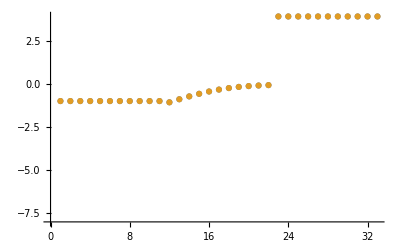

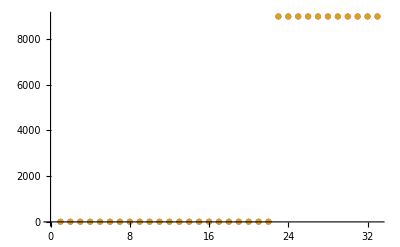

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

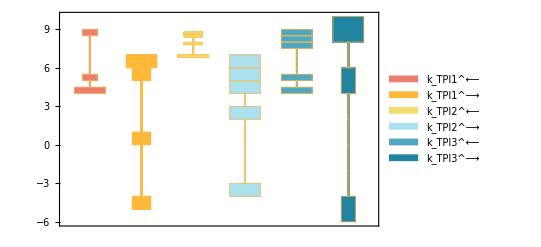

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

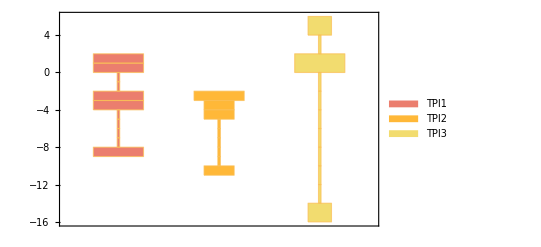

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

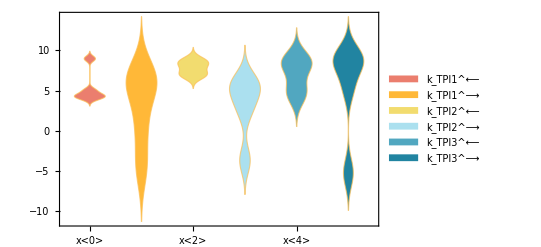

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

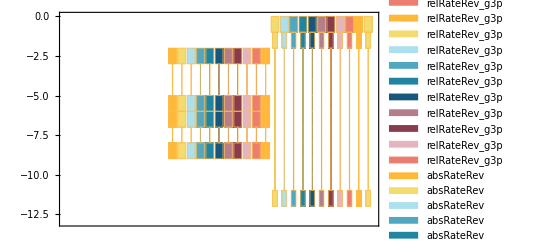

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 5;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.00103 | 0.000502615 | 51.2024

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
9000 | 8999.99 | 0.000126519

```mathematica
backCalculateRatios[haldaneDataList[[1]][[1]], haldaneDataList[[1]][[2]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
0.107411 | 0.107412 | 0.000953614